#### Parameters Setup.

```mathematica
k=1.5;
sampleSize=200;
trajLen=100;
thetaMin=0.;
thetaMax=2.π;
pMin=0.;
pMax=2.π;
```

#### Evolution

```mathematica
thLis={RandomReal[{thetaMin,thetaMax},{sampleSize}]};
pLis={RandomReal[{pMin,pMax},{sampleSize}]};
Do[
AppendTo[pLis,Mod[pLis[[-1]]+k*Sin[thLis[[-1]]],2.*π]];
AppendTo[thLis,Mod[thLis[[-1]]+pLis[[-1]],2.*π]];
,{trajLen}]
```

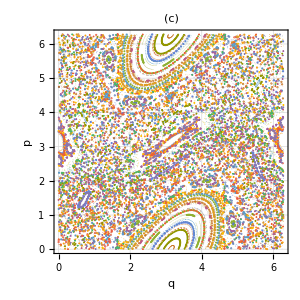

```mathematica
tb=Table[Transpose[{thLis[[;;,i]],pLis[[;;,i]]}],{i,1,sampleSize}];
k15c=ListPlot[tb[[;;,;;]],
{PlotTheme->"Detailed",AspectRatio->1,PlotLabel->"(c)",
FrameLabel->{"q","p"},
ImageSize->300,
FrameStyle->15,
PlotMarkers->{Automatic,0.2}
}]
```

#### Momentum Distribution

```mathematica
thLis={RandomReal[{thetaMin,thetaMax},{sampleSize}]};
pLis={RandomReal[{pMin,pMax},{sampleSize}]};
Do[
AppendTo[pLis,pLis[[-1]]+K*Sin[thLis[[-1]]]];
AppendTo[thLis,Mod[thLis[[-1]]+pLis[[-1]],2.*π]];
,{trajLen}]
```

```mathematica
Manipulate[Histogram[pLis[[time]]],{time,1,trajLen,1}]
```

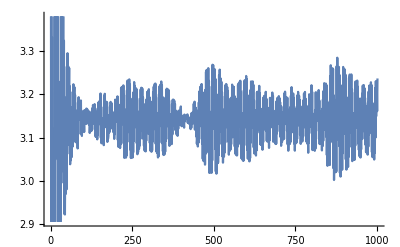

```mathematica
ListLinePlot[Mean/@pLis]
```

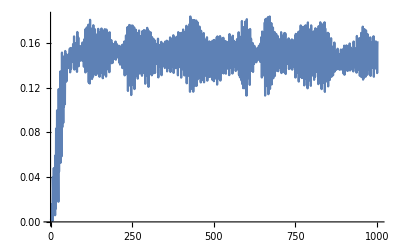

```mathematica
ListLinePlot[Variance/@pLis]
```